## Initialization

```mathematica
Clear["Global`*"]
```

Approximate value of fN

```mathematica
Module[{a0=6, R,N=121, fa0, G, Acell, L}, 
R = 0.2*a0;
fa0 = Sinh[R]Exp[R-a0]/a0;
G = 2π Exp[R] Sinh[R];
Acell = Sqrt[3]/2 a0^2;
L = Sqrt[ (N-7)Acell/π + (a0/2)^2];
fNest = 6fa0+G/Acell(Exp[-1.5 a0]- Exp[-L]);
Print[fNest];
fNinf = 6fa0+G/Acell Exp[-1.5 a0];
Print[fNinf];
];
params = {fN-> fNinf, n-> 2};
```

0.0125471

0.0125471

Exact values for fN
N=121, a0 = 0.5 => 
N=121, a0 = 1.5 =>

```mathematica
Yself[X_]:= (Con-1)X+1;
Ynei[Xm_]:= fN*((Con-1)*Xm + 1);
```

## n=1 solution

```mathematica
S[X_]:= (Con-1)X + 1;
sol=Xcell/.Solve[(S[Xcell]+fN S[Xmf])/(k + S[Xcell]+fN S[Xmf])== Xcell, {Xcell}]
```

{(2-Con+fN+k-fN Xmf+Con fN Xmf-√((-2+Con-fN-k+fN Xmf-Con fN Xmf)^2-4 (1-Con) (1+fN-fN Xmf+Con fN Xmf)))/(2 (1-Con)),(2-Con+fN+k-fN Xmf+Con fN Xmf+√((-2+Con-fN-k+fN Xmf-Con fN Xmf)^2-4 (1-Con) (1+fN-fN Xmf+Con fN Xmf)))/(2 (1-Con))}

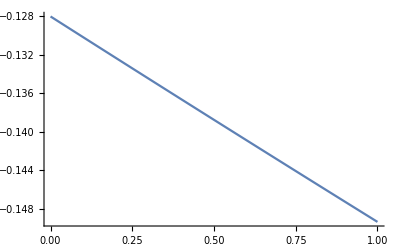

```mathematica
Plot[sol[[2]] /. {fN-> fNinf,Con-> 16, k-> 8}, {Xmf,0,1}]
```

## Mean field dynamical solution

Solve for steady state of mean-field evolution assuming eventual homogenisation.
No general solution for arbitrary n.

```mathematica
Solve[X == (c*(a*X+b))^n/(k^n + (c*(a*X+b))^n) /. {n-> 3/2}, X]
```

{{X→Root[b^3 c^3+(3 a b^2 c^3-2 b^3 c^3) #1+(3 a^2 b c^3-6 a b^2 c^3+b^3 c^3-k^3) #1^2+(a^3 c^3-6 a^2 b c^3+3 a b^2 c^3) #1^3+(-2 a^3 c^3+3 a^2 b c^3) #1^4+a^3 c^3 #1^5&,1]},{X→Root[b^3 c^3+(3 a b^2 c^3-2 b^3 c^3) #1+(3 a^2 b c^3-6 a b^2 c^3+b^3 c^3-k^3) #1^2+(a^3 c^3-6 a^2 b c^3+3 a b^2 c^3) #1^3+(-2 a^3 c^3+3 a^2 b c^3) #1^4+a^3 c^3 #1^5&,2]},{X→Root[b^3 c^3+(3 a b^2 c^3-2 b^3 c^3) #1+(3 a^2 b c^3-6 a b^2 c^3+b^3 c^3-k^3) #1^2+(a^3 c^3-6 a^2 b c^3+3 a b^2 c^3) #1^3+(-2 a^3 c^3+3 a^2 b c^3) #1^4+a^3 c^3 #1^5&,3]},{X→Root[b^3 c^3+(3 a b^2 c^3-2 b^3 c^3) #1+(3 a^2 b c^3-6 a b^2 c^3+b^3 c^3-k^3) #1^2+(a^3 c^3-6 a^2 b c^3+3 a b^2 c^3) #1^3+(-2 a^3 c^3+3 a^2 b c^3) #1^4+a^3 c^3 #1^5&,4]},{X→Root[b^3 c^3+(3 a b^2 c^3-2 b^3 c^3) #1+(3 a^2 b c^3-6 a b^2 c^3+b^3 c^3-k^3) #1^2+(a^3 c^3-6 a^2 b c^3+3 a b^2 c^3) #1^3+(-2 a^3 c^3+3 a^2 b c^3) #1^4+a^3 c^3 #1^5&,5]}}

Brute force solving difference equation. Works for n=1, probably not for any other n. Mean-field solution does not go to mean field value.

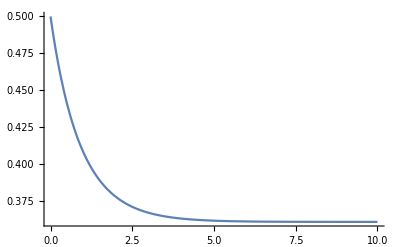

```mathematica
S[x_]:= Coff + (Con-Coff)*x;sol=RSolve[{ X[t+1] == (S[X[t]] + fN  S[Xm] )^n/(k^n + (S[X[t]] + fN S[Xm] )^n) /. {n-> 1}, X[0]==x0 }, X[t], t];
params  ={k-> 10, Coff-> 1, Con-> 10, fN-> 0.5, n-> 1.5, x0-> 0.5, Xm-> 0.2};
Plot[ X[t] /. sol[[1]] /. params , {t,0,10}, PlotRange-> All]
```

### Numerical solutions

Model as difference equation

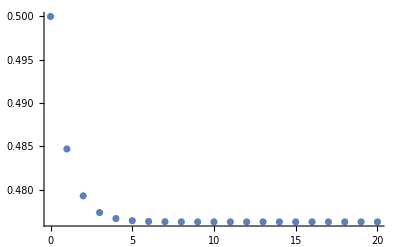

```mathematica
params  ={k-> 10, Coff-> 1, Con-> 10, fN-> 0.5, n-> 1.5, x0-> 0.5, Xm-> 0.8};
tmax=20;
solvals=RecurrenceTable[{ X[t+1] == (S[X[t]] + fN S[Xm] )^n/(k^n + (S[X[t]] + fN S[Xm] )^n), X[0]==x0 }/. params, X[t], {t, 0, tmax}];
ListPlot[Transpose[{Range[0, tmax], solvals}], PlotRange-> All]
```

## Number of fixed points

### Analytical solutions are not very useful

Strategy: 
(1) obtain analytical solution for n=2 (cubic equation).
(2) get number of well-defined solutions for given parameter range. Take max. over Xm ∈ [0,1].
(3) loop over parameter range to generate heat map of number of solutions.

General analytical solution for fixed K, Con

```mathematica
sol=Solve[(Ynei[Xm]+Yself[X])^n/(k^n + (Ynei[Xm]+Yself[X])^n)-X == 0 /. params, X,Reals];
Length[sol /. {k-> 8 ,Con-> 16}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

3

### Loop over K, Con range and calculate

Test some results

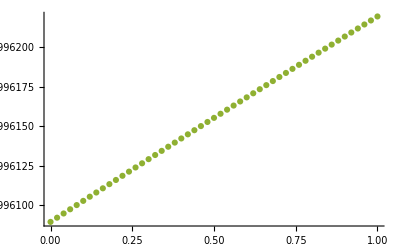

```mathematica
sols0 =Quiet@Table[ X /.Solve[(Ynei[Xm]+Yself[X])^n/(k^n + (Ynei[Xm]+Yself[X])^n)-X == 0 /.params/.{ Con-> 16, k-> 1,Xm-> xm}], {xm,0,1,0.02}];
ListPlot[Transpose[{Range[0,1,0.02],#}]&/@Transpose[sols0]]
```

```mathematica
step=1;
Krange=Range[1,20,step];
Conrange = Range[1,30,step];
calcnsol[Kin_,Conin_]:=Module[{sols0, sols, nsols, dx= 0.05},
sols0 =Quiet@Table[ X /.Solve[(Ynei[Xm]+Yself[X])^n/(k^n + (Ynei[Xm]+Yself[X])^n)-X == 0 /.params/.{ Con-> Conin, k-> Kin,Xm-> xm}], {xm,0,1,dx}];
sols=Map[DeleteCases[#, Undefined]&, sols0];
nsols=Length/@sols;
Max[nsols]
];
nsolmap=Table[calcnsol[Krange[[i]], Conrange[[j]]],{j,1,Length[Conrange]}, {i,1,Length[Krange]}];
Print[TableForm@nsolmap];
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3

Plot map

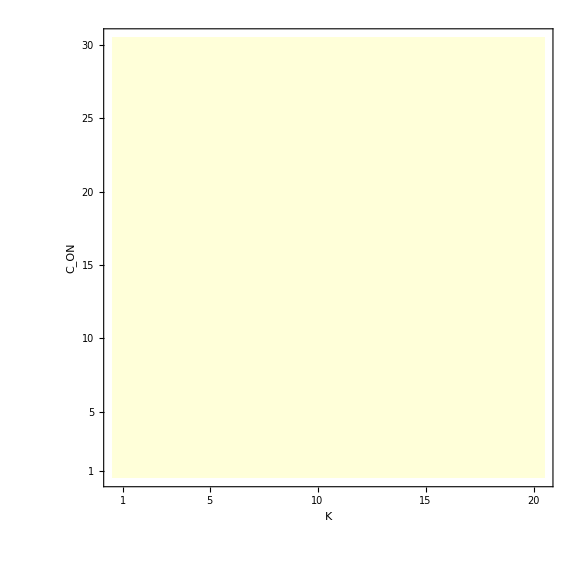

```mathematica
tick1[n_]:= {(n-1)/step+1,Krange[[(n-1)/step+1]]};
tick2[n_]:= {(n-1)/step+1,Conrange[[(n-1)/step+1]]};
hticks = { {tick1[1], tick1[5], tick1[10], tick1[15], tick1[20]}, None};
vticks ={ {tick2[1], tick2[5], tick2[10], tick2[15], tick2[20],  tick2[25],  tick2[30]}, None};
ticks={vticks,hticks};
plot = ArrayPlot[nsolmap, DataReversed -> True, ImageSize-> Large,BaseStyle->{FontSize-> 24},Frame-> True, FrameLabel-> {"C_ON","K"}, FrameTicks-> ticks, ColorRules->{1->Blue,3->LightYellow}, AspectRatio->1]
```

### Export plot

```mathematica
fnamestr = StringReplace["mean_field_bistable_lattice_K_Con_map_hill_var1_a0_var2.pdf",{"var1"->"2","var2"-> "6"}];
fname=FileNameJoin[{NotebookDirectory[], "fixed_points_mean_field",fnamestr}];
Export[fname,plot]
```

H:\My Documents\Multicellular automaton\Mathematica calculations\fixed_points_mean_field\mean_field_bistable_lattice_K_Con_map_hill_2_a0_6.pdf